```mathematica
1/Sqrt[Det[{{12,1},{1,2}}]]
```

1/(√23)

```mathematica
1/Sqrt[Det[{{2,1},{1,2}}]]
```

1/(√3)

```mathematica
{{3,2},{2,3}}.{{a,b},{2,3}}
```

{{4+3 a,6+3 b},{6+2 a,9+2 b}}

```mathematica
Inverse[{{3,2},{2,3}}]
```

{{3/5,-2/5},{-2/5,3/5}}

```mathematica
Flatten[{{13}}]
```

{13}

```mathematica
Transpose[{{a},{b}}-{{3},{6}}].Inverse[{{12,1},{1,2}}].({{a},{b}}-{{3},{6}})-
Transpose[{{a},{b}}-{{13},{10}}].Inverse[{{2,1},{1,2}}].({{a},{b}}-{{13},{10}})
```

{{(-3+a) (2/23 (-3+a)+(6-b)/23)-(-13+a) (2/3 (-13+a)+(10-b)/3)-((13-a)/3+2/3 (-10+b)) (-10+b)+((3-a)/23+12/23 (-6+b)) (-6+b)}}

```mathematica
Flatten[{{(-3+a) (2/23 (-3+a)+(6-b)/23)-(-13+a) (2/3 (-13+a)+(10-b)/3)-((13-a)/3+2/3 (-10+b)) (-10+b)+((3-a)/23+12/23 (-6+b)) (-6+b)}}]
```

{(-3+a) (2/23 (-3+a)+(6-b)/23)-(-13+a) (2/3 (-13+a)+(10-b)/3)-((13-a)/3+2/3 (-10+b)) (-10+b)+((3-a)/23+12/23 (-6+b)) (-6+b)}

```mathematica
{{a},{b}}-{{3},{6}}
```

{{-3+a},{-6+b}}

```mathematica
MatrixForm[{{-3+a},{-6+b}}]
```

(-3+a
-6+b)

```mathematica
Transpose[{{-3+a},{-6+b}}]
```

{{-3+a,-6+b}}

```mathematica
MatrixForm[{{-3+a,-6+b}}]
```

(-3+a | -6+b)

```mathematica
(-3+a) (2/23 (-3+a)+(6-b)/23)-(-13+a) (2/3 (-13+a)+(10-b)/3)-((13-a)/3+2/3 (-10+b)) (-10+b)+((3-a)/23+12/23 (-6+b)) (-6+b)
```

(-3+a) (2/23 (-3+a)+(6-b)/23)-(-13+a) (2/3 (-13+a)+(10-b)/3)-((13-a)/3+2/3 (-10+b)) (-10+b)+((3-a)/23+12/23 (-6+b)) (-6+b)

```mathematica
Simplify[(-3+a) (2/23 (-3+a)+(6-b)/23)-(-13+a) (2/3 (-13+a)+(10-b)/3)-((13-a)/3+2/3 (-10+b)) (-10+b)+((3-a)/23+12/23 (-6+b)) (-6+b)]
```

-2/69 (2576+20 a^2+46 b+5 b^2-4 a (92+5 b))

```mathematica
Plot3D[-2/69 (2576+20 a^2+46 b+5 b^2-4 a (92+5 b)),{a,-0.140625,0.140625},{b,-2.3934375,2.3934375}]
```

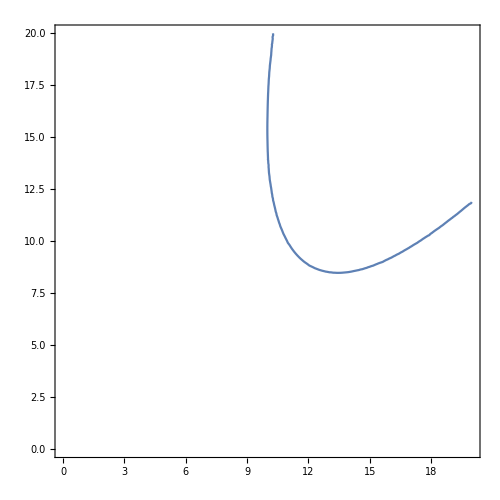

```mathematica
ContourPlot[1/18*Sqrt[23/3]*Exp[-1/69 (2576+20 a^2+46 b+5 b^2-4 a (92+5 b))]==10,{a,0,20},{b,0,20},ImageSize->{500,500}]
```